Here, we use the same data from Figure 3, but zoom in on the pinning of the (quasi)uniform mode.

This is used to make Figure 4 of the article.

## The Eigenfrequencies -- D = 4.2 mJ/m^2 on top surface only

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=16;  (* 16 atomic layers *)
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=835563; (*A/m*)
AA=1.355 10^-11;  (*J/m*)
DD =4.2 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

527.335

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[LL]=0
```

0

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

## Mode profiles of PSSWs

Functions to extract and plot the PSSW mode profiles.

```mathematica
modefunxions[NN_,y_,z_,β_]:=modefunxions[NN,y,z,β]=Chop[Table[Reverse[Eigenvectors[big[NN,y,z,β]]]⟦k⟧,{k,1,2 NN,1}]];
```

```mathematica
xmotion[NN_,y_,z_,β_,k_]:=xmotion[NN,y,z,β,k]=Table[modefunxions[NN,y,z,β]⟦k⟧⟦n⟧,{n,1,2 NN,2}]
ymotion[NN_,y_,z_,β_,k_]:=ymotion[NN,y,z,β,k]=Table[modefunxions[NN,y,z,β]⟦k⟧⟦n⟧,{n,2,2 NN,2}]
```

```mathematica
px1[NN_,ky_,k_]:=px1[NN,ky,k]=ListPlot[xmotion[NN,ky a,0,0.5,k],PlotRange->All,PlotStyle->Hue[0.4],PlotLabel->Abs[freqs2[NN,ky a,0,0.5]]⟦k⟧];
py1[NN_,ky_,k_]:=py1[NN,ky,k]=ListPlot[ymotion[NN,ky a,0,0.5,k],PlotRange->All,PlotStyle->Hue[0],PlotLabel->Abs[freqs2[NN,ky a,0,0.5]]⟦k⟧];
pimag1[NN_,ky_,k_]:=pimag1[NN,ky,k]=ListPlot[ⅈ xmotion[NN,ky a,0,0.5,k],PlotRange->All,PlotStyle->Hue[0.7],PlotLabel->Abs[freqs2[NN,ky a,0,0.5]]⟦k⟧];
```

```mathematica
modefunxions[LL,20 10^6,0,0.5];
```

```mathematica
freqs2[LL,20 10^6 a,0,0.5]
```

{-5.71702,6.42102,-582.681,584.075,-2263.99,2265.34,-4994.08,4995.37,-8668.14,8669.34,-13145.,13146.1,-18252.6,18253.6,-23794.7,23795.5,-29558.2,29558.9,-35321.8,35322.3,-40863.8,40864.3,-45971.4,45971.7,-50448.3,50448.5,-54122.3,54122.4,-56852.4,56852.4,-58533.6,58533.6}

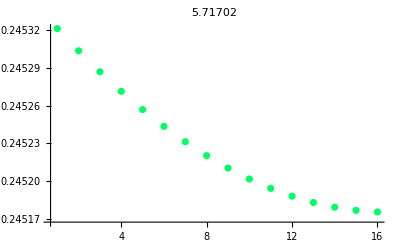

```mathematica
px1[LL,20 10^6,1]
```

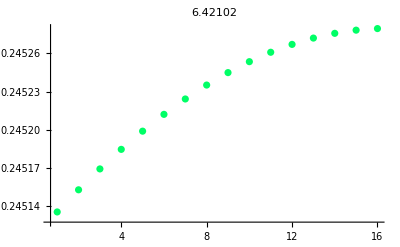

```mathematica
px1[LL,20 10^6,2]
```

```mathematica
6.42102-5.71702
```

0.704

```mathematica
xmotion[LL,20 10^6 a,0,0.5,1]
```

{0.245321,0.245304,0.245287,0.245271,0.245257,0.245244,0.245231,0.24522,0.24521,0.245202,0.245194,0.245188,0.245183,0.245179,0.245177,0.245176}

Normalizing :

```mathematica
uniformNegkx=xmotion[LL,20 10^6 a,0,0.5,1]/0.24517555734108742
```

{1.00059,1.00052,1.00045,1.00039,1.00033,1.00028,1.00023,1.00018,1.00014,1.00011,1.00008,1.00005,1.00003,1.00002,1.00001,1.}

Other mode:

```mathematica
xmotion[LL,20 10^6 a,0,0.5,2]
```

{0.245135,0.245153,0.245169,0.245185,0.245199,0.245212,0.245224,0.245235,0.245245,0.245254,0.245261,0.245267,0.245272,0.245276,0.245278,0.24528}

```mathematica
uniformPoskx=xmotion[LL,20 10^6 a,0,0.5,2]/0.2452795646287667
```

{0.999413,0.999484,0.99955,0.999613,0.999671,0.999725,0.999774,0.999819,0.999859,0.999894,0.999924,0.999949,0.99997,0.999985,0.999995,1.}

Try the next mode (first exchange mode with one node, n=1):

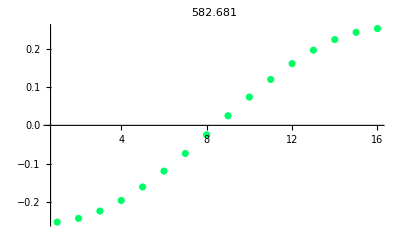

```mathematica
px1[LL,20 10^6,3]
```

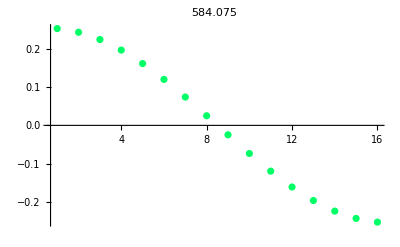

```mathematica
px1[LL,20 10^6,4]
```

## Pinning of the uniform mode -- zoom in

By running the code above for the case of
(i) no DMI
(2) DMI with kx=+20 μm^-1
(3) DMI with kx=-20 μm^-1
we get the following mode profiles for the 16 atomic layers in the thickness direction, normalized to 1 on the bottom edge:

```mathematica
uniform={1.0000000000000078,1.0000000000000084,1.00000000000001,1.0000000000000102,1.0000000000000113,1.0000000000000102,1.0000000000000093,1.0000000000000073,1.000000000000006,1.0000000000000042,1.000000000000003,1.0000000000000022,1.0000000000000007,1.0000000000000002,0.9999999999999997,1.};
```

```mathematica
uniformPoskx={0.9994126277726905,0.9994835793398625,0.9995504457161835,0.9996130901747001,0.9996713869428284,0.9997252209326898,0.9997744874943625,0.9998190921915322,0.9998589505990523,0.9998939881219806,0.9999241398356828,0.9999493503466921,0.9999695736739797,0.9999847731504135,0.9999949213441804,1.};
uniformNegkx={1.000594872803094,1.0005227021836753,1.0004547714453609,1.0003912017790881,1.000332104655793,1.0002775820677572,1.0002277267494373,1.000182622378267,1.0001423437558634,1.0001069569700207,1.0000765195378378,1.0000510805303007,1.0000306806785622,1.00001535246217,1.000005120179421,0.9999999999999999};
```

Now to plot these so they look like they are through the thickness:

```mathematica
uniform2=Table[{uniform[[i]],17-i},{i,1,Length[uniform]}];
uniformPoskx2=Table[{uniformPoskx[[i]],17-i},{i,1,Length[uniform]}];
uniformNegkx2=Table[{uniformNegkx[[i]],17-i},{i,1,Length[uniform]}];
```

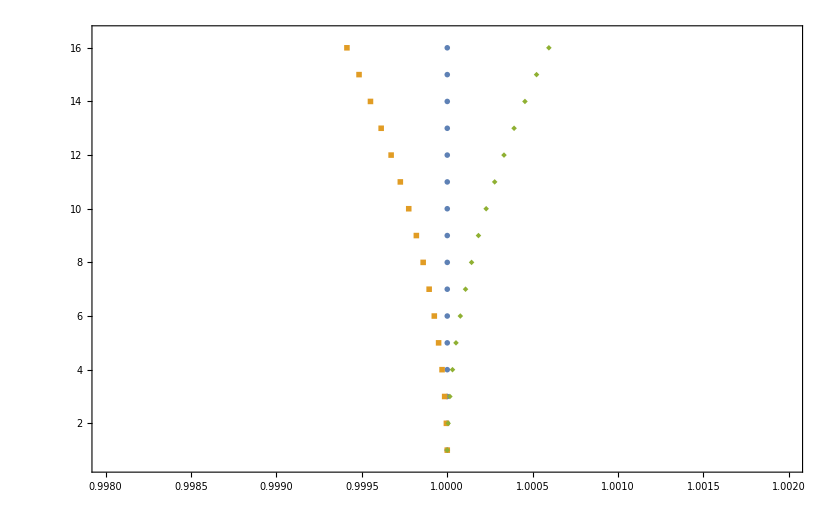

```mathematica
pinninggg=ListPlot[{uniform2, uniformPoskx2,uniformNegkx2},PlotRange->{{0.998,1.002},{0.5,16.5}},PlotMarkers->{Automatic,0.04},Frame->{{False,False},{True,True}},FrameStyle->Directive[Black,Bold,Thickness[0.005]],LabelStyle->{FontFamily->"Times",FontSize->50},ImageSize->1000]
```

```mathematica
Export["/Users/karen/Desktop/UON stuff/Students/Ellen/Spin waves DMI/Figures/Pinning.png",pinninggg]
```

/Users/karen/Desktop/UON stuff/Students/Ellen/Spin waves DMI/Figures/Pinning.png

Instead, I can normalize a different way (normalization is arbitrary) so that these look more like traveling waves with surface pinning:

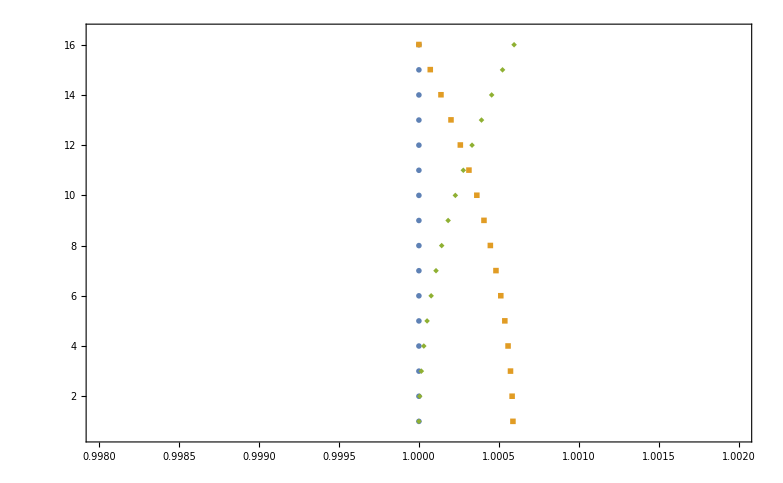

```mathematica
pinninggg=ListPlot[{uniform2, uniformPoskx2/0.9994126277726905,uniformNegkx2},PlotRange->{{0.998,1.002},{0.5,16.5}},PlotMarkers->{Automatic,0.04},Frame->{{False,False},{True,True}},FrameStyle->Directive[Black,Bold,Thickness[0.005]],LabelStyle->{FontFamily->"Times",FontSize->50},ImageSize->1000]
```